### Calculate coefficient of determination function

```mathematica
CoefficientRR[ y_, f_]:= 1 - (#.#&[y - f ])/(#.#&[y - Mean[y]])(*Формула для вычисления коэффициента детерминации*)
```

## Data import and formatting

```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["summary_SDB (1).xlsx"];
rawData =rawData⟦1⟧
```

{{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,Medium with 5% FBS,,,,,,,,,,,,,,,Serum-free medium,,,,,,,,,,,,,},{,,,Luminescence (RLU),,,,,,,Fluorescence (RFU),,,,,,,,Luminescence (RLU),,,,,,,Fluorescence (RFU),,,,,,},{Tme point,Date,Time (h),50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC},{T0,20.07.2022 21:35:59,0.,1.17887×10^6,1.1992×10^6,1.46962×10^6,1.44045×10^6,1.40745×10^6,1.21322×10^6,4299.,30.3983,44.9908,30.2558,32.5633,31.4208,28.5118,0.807667,,908694.,1.17092×10^6,1.16969×10^6,1.09737×10^6,1.08577×10^6,881344.,4797.33,7.44808,8.83483,11.2198,12.4548,15.4123,24.5023,57.594},{T1,21.07.2022 00:34:55,3.,2.3114×10^6,2.3044×10^6,3.05715×10^6,2.9089×10^6,2.8469×10^6,2.4469×10^6,2670.33,37.014,53.0465,39.599,47.154,42.819,35.8743,1.08567,,771995.,2.41034×10^6,2.28359×10^6,2.19109×10^6,2.10184×10^6,1.58434×10^6,853.667,16.7827,13.0865,14.405,24.3165,28.464,41.7465,70.639},{T2,21.07.2022 09:57:58,12.5,2.93206×10^6,2.68181×10^6,3.79406×10^6,3.73956×10^6,3.84281×10^6,3.42456×10^6,0.,45.9522,66.1472,45.8047,50.9122,30.0397,23.7779,3.007,,232397.,1.67332×10^6,1.0539×10^6,967897.,957522.,806047.,55.4,43.2007,22.3737,19.7857,27.2857,24.1882,24.9257,85.2007},{T3,21.07.2022 12:56:33,15.5,2.84842×10^6,2.67469×10^6,3.60092×10^6,3.70417×10^6,3.93842×10^6,3.44377×10^6,0.,44.0888,65.2188,45.6438,53.2038,38.6013,29.4951,2.34333,,120550.,1.3036×10^6,860030.,776655.,842805.,717230.,0.,43.7907,22.8857,21.3032,28.6182,29.1707,32.6557,87.0807},{T4,21.07.2022 15:53:44,18.5,3.18434×10^6,2.98322×10^6,3.89959×10^6,4.17634×10^6,4.53809×10^6,4.05559×10^6,0.,40.2593,62.2343,45.4143,54.2593,47.8193,38.2121,1.075,,81039.2,1.05462×10^6,871967.,806692.,893517.,733967.,0.,41.801,27.031,22.0335,33.491,36.166,47.4935,81.6393},{T5,21.07.2022 18:55:34,21.5,2.9683×10^6,2.81913×10^6,3.6533×10^6,3.8593×10^6,4.4423×10^6,3.92903×10^6,0.,39.767,60.592,44.5145,52.6395,49.662,37.6188,1.008,,46720.4,745948.,757093.,711943.,767793.,668768.,0.,41.4375,29.7085,20.8975,32.7125,37.4775,50.55,81.2833},{T6,21.07.2022 21:54:22,24.5,3.25796×10^6,3.10929×10^6,3.90996×10^6,4.18646×10^6,4.90546×10^6,4.10746×10^6,0.,39.4223,59.7398,45.2298,54.3573,49.5548,37.9301,1.04767,,39220.,668983.,765910.,748510.,788060.,680760.,0.,42.2303,32.1883,23.1953,34.6928,38.8103,48.2403,78.2287},{T7,22.07.2022 00:44:51,27.5,3.24315×10^6,3.10823×10^6,3.86515×10^6,4.1689×10^6,4.9534×10^6,4.28653×10^6,0.,39.276,59.3485,46.071,55.606,49.7385,37.6653,0.978,,28122.6,531915.,640313.,710613.,718413.,625738.,0.,43.2462,35.1487,27.3087,36.2762,39.6337,47.8487,82.6203},{T8,22.07.2022 17:11:06,44.,2.98127×10^6,2.95581×10^6,3.04519×10^6,3.89672×10^6,4.82422×10^6,4.14497×10^6,0.,35.7735,54.966,49.8835,57.526,47.126,36.7523,0.940667,,7739.7,145377.,210494.,366297.,397847.,345172.,0.,41.488,49.238,42.2605,44.263,39.388,48.6355,67.1447},{T9,22.07.2022 20:08:28,47.,3.20472×10^6,3.02563×10^6,3.14014×10^6,3.99563×10^6,4.86963×10^6,4.51938×10^6,0.,33.1602,54.4252,46.8077,55.5402,45.6952,35.8172,0.828333,,5951.58,89010.8,129641.,261801.,322789.,276714.,0.,40.9165,51.259,43.139,46.229,39.9965,48.564,67.2907},{T10,22.07.2022 22:58:02,50.,2.76678×10^6,2.72165×10^6,2.83391×10^6,3.50461×10^6,4.29301×10^6,4.10276×10^6,0.,32.9665,53.774,45.8065,55.9265,45.3765,36.336,0.908667,,5694.29,52343.9,79806.4,202143.,283198.,240773.,0.,40.6153,54.2678,45.3353,48.4903,40.6728,47.6853,67.262},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.284138,0.29669,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.574736,0.617182,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.775792,0.76595,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.795093,0.726958,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.916157,0.787256,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.896819,0.737534,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.990322,0.789349,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,1.,0.780302,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.97392,0.614767,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.983087,0.633935,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.866678,0.572114,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}}

```mathematica
rawData//MatrixForm
```

( |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Medium with 5% FBS |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Serum-free medium |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  | 
Tme point | Date | Time (h) | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC |  | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC
T0 | 20.07.2022 21:35:59 | 0. | 1.17887×10^6 | 1.1992×10^6 | 1.46962×10^6 | 1.44045×10^6 | 1.40745×10^6 | 1.21322×10^6 | 4299. | 30.3983 | 44.9908 | 30.2558 | 32.5633 | 31.4208 | 28.5118 | 0.807667 |  | 908694. | 1.17092×10^6 | 1.16969×10^6 | 1.09737×10^6 | 1.08577×10^6 | 881344. | 4797.33 | 7.44808 | 8.83483 | 11.2198 | 12.4548 | 15.4123 | 24.5023 | 57.594
T1 | 21.07.2022 00:34:55 | 3. | 2.3114×10^6 | 2.3044×10^6 | 3.05715×10^6 | 2.9089×10^6 | 2.8469×10^6 | 2.4469×10^6 | 2670.33 | 37.014 | 53.0465 | 39.599 | 47.154 | 42.819 | 35.8743 | 1.08567 |  | 771995. | 2.41034×10^6 | 2.28359×10^6 | 2.19109×10^6 | 2.10184×10^6 | 1.58434×10^6 | 853.667 | 16.7827 | 13.0865 | 14.405 | 24.3165 | 28.464 | 41.7465 | 70.639
T2 | 21.07.2022 09:57:58 | 12.5 | 2.93206×10^6 | 2.68181×10^6 | 3.79406×10^6 | 3.73956×10^6 | 3.84281×10^6 | 3.42456×10^6 | 0. | 45.9522 | 66.1472 | 45.8047 | 50.9122 | 30.0397 | 23.7779 | 3.007 |  | 232397. | 1.67332×10^6 | 1.0539×10^6 | 967897. | 957522. | 806047. | 55.4 | 43.2007 | 22.3737 | 19.7857 | 27.2857 | 24.1882 | 24.9257 | 85.2007
T3 | 21.07.2022 12:56:33 | 15.5 | 2.84842×10^6 | 2.67469×10^6 | 3.60092×10^6 | 3.70417×10^6 | 3.93842×10^6 | 3.44377×10^6 | 0. | 44.0888 | 65.2188 | 45.6438 | 53.2038 | 38.6013 | 29.4951 | 2.34333 |  | 120550. | 1.3036×10^6 | 860030. | 776655. | 842805. | 717230. | 0. | 43.7907 | 22.8857 | 21.3032 | 28.6182 | 29.1707 | 32.6557 | 87.0807
T4 | 21.07.2022 15:53:44 | 18.5 | 3.18434×10^6 | 2.98322×10^6 | 3.89959×10^6 | 4.17634×10^6 | 4.53809×10^6 | 4.05559×10^6 | 0. | 40.2593 | 62.2343 | 45.4143 | 54.2593 | 47.8193 | 38.2121 | 1.075 |  | 81039.2 | 1.05462×10^6 | 871967. | 806692. | 893517. | 733967. | 0. | 41.801 | 27.031 | 22.0335 | 33.491 | 36.166 | 47.4935 | 81.6393
T5 | 21.07.2022 18:55:34 | 21.5 | 2.9683×10^6 | 2.81913×10^6 | 3.6533×10^6 | 3.8593×10^6 | 4.4423×10^6 | 3.92903×10^6 | 0. | 39.767 | 60.592 | 44.5145 | 52.6395 | 49.662 | 37.6188 | 1.008 |  | 46720.4 | 745948. | 757093. | 711943. | 767793. | 668768. | 0. | 41.4375 | 29.7085 | 20.8975 | 32.7125 | 37.4775 | 50.55 | 81.2833
T6 | 21.07.2022 21:54:22 | 24.5 | 3.25796×10^6 | 3.10929×10^6 | 3.90996×10^6 | 4.18646×10^6 | 4.90546×10^6 | 4.10746×10^6 | 0. | 39.4223 | 59.7398 | 45.2298 | 54.3573 | 49.5548 | 37.9301 | 1.04767 |  | 39220. | 668983. | 765910. | 748510. | 788060. | 680760. | 0. | 42.2303 | 32.1883 | 23.1953 | 34.6928 | 38.8103 | 48.2403 | 78.2287
T7 | 22.07.2022 00:44:51 | 27.5 | 3.24315×10^6 | 3.10823×10^6 | 3.86515×10^6 | 4.1689×10^6 | 4.9534×10^6 | 4.28653×10^6 | 0. | 39.276 | 59.3485 | 46.071 | 55.606 | 49.7385 | 37.6653 | 0.978 |  | 28122.6 | 531915. | 640313. | 710613. | 718413. | 625738. | 0. | 43.2462 | 35.1487 | 27.3087 | 36.2762 | 39.6337 | 47.8487 | 82.6203
T8 | 22.07.2022 17:11:06 | 44. | 2.98127×10^6 | 2.95581×10^6 | 3.04519×10^6 | 3.89672×10^6 | 4.82422×10^6 | 4.14497×10^6 | 0. | 35.7735 | 54.966 | 49.8835 | 57.526 | 47.126 | 36.7523 | 0.940667 |  | 7739.7 | 145377. | 210494. | 366297. | 397847. | 345172. | 0. | 41.488 | 49.238 | 42.2605 | 44.263 | 39.388 | 48.6355 | 67.1447
T9 | 22.07.2022 20:08:28 | 47. | 3.20472×10^6 | 3.02563×10^6 | 3.14014×10^6 | 3.99563×10^6 | 4.86963×10^6 | 4.51938×10^6 | 0. | 33.1602 | 54.4252 | 46.8077 | 55.5402 | 45.6952 | 35.8172 | 0.828333 |  | 5951.58 | 89010.8 | 129641. | 261801. | 322789. | 276714. | 0. | 40.9165 | 51.259 | 43.139 | 46.229 | 39.9965 | 48.564 | 67.2907
T10 | 22.07.2022 22:58:02 | 50. | 2.76678×10^6 | 2.72165×10^6 | 2.83391×10^6 | 3.50461×10^6 | 4.29301×10^6 | 4.10276×10^6 | 0. | 32.9665 | 53.774 | 45.8065 | 55.9265 | 45.3765 | 36.336 | 0.908667 |  | 5694.29 | 52343.9 | 79806.4 | 202143. | 283198. | 240773. | 0. | 40.6153 | 54.2678 | 45.3353 | 48.4903 | 40.6728 | 47.6853 | 67.262
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.284138 | 0.29669 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.574736 | 0.617182 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.775792 | 0.76595 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.795093 | 0.726958 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.916157 | 0.787256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.896819 | 0.737534 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.990322 | 0.789349 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1. | 0.780302 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.97392 | 0.614767 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.983087 | 0.633935 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.866678 | 0.572114 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
data = rawData⟦4;;15⟧
```

{{Tme point,Date,Time (h),50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC},{T0,20.07.2022 21:35:59,0.,1.17887×10^6,1.1992×10^6,1.46962×10^6,1.44045×10^6,1.40745×10^6,1.21322×10^6,4299.,30.3983,44.9908,30.2558,32.5633,31.4208,28.5118,0.807667,,908694.,1.17092×10^6,1.16969×10^6,1.09737×10^6,1.08577×10^6,881344.,4797.33,7.44808,8.83483,11.2198,12.4548,15.4123,24.5023,57.594},{T1,21.07.2022 00:34:55,3.,2.3114×10^6,2.3044×10^6,3.05715×10^6,2.9089×10^6,2.8469×10^6,2.4469×10^6,2670.33,37.014,53.0465,39.599,47.154,42.819,35.8743,1.08567,,771995.,2.41034×10^6,2.28359×10^6,2.19109×10^6,2.10184×10^6,1.58434×10^6,853.667,16.7827,13.0865,14.405,24.3165,28.464,41.7465,70.639},{T2,21.07.2022 09:57:58,12.5,2.93206×10^6,2.68181×10^6,3.79406×10^6,3.73956×10^6,3.84281×10^6,3.42456×10^6,0.,45.9522,66.1472,45.8047,50.9122,30.0397,23.7779,3.007,,232397.,1.67332×10^6,1.0539×10^6,967897.,957522.,806047.,55.4,43.2007,22.3737,19.7857,27.2857,24.1882,24.9257,85.2007},{T3,21.07.2022 12:56:33,15.5,2.84842×10^6,2.67469×10^6,3.60092×10^6,3.70417×10^6,3.93842×10^6,3.44377×10^6,0.,44.0888,65.2188,45.6438,53.2038,38.6013,29.4951,2.34333,,120550.,1.3036×10^6,860030.,776655.,842805.,717230.,0.,43.7907,22.8857,21.3032,28.6182,29.1707,32.6557,87.0807},{T4,21.07.2022 15:53:44,18.5,3.18434×10^6,2.98322×10^6,3.89959×10^6,4.17634×10^6,4.53809×10^6,4.05559×10^6,0.,40.2593,62.2343,45.4143,54.2593,47.8193,38.2121,1.075,,81039.2,1.05462×10^6,871967.,806692.,893517.,733967.,0.,41.801,27.031,22.0335,33.491,36.166,47.4935,81.6393},{T5,21.07.2022 18:55:34,21.5,2.9683×10^6,2.81913×10^6,3.6533×10^6,3.8593×10^6,4.4423×10^6,3.92903×10^6,0.,39.767,60.592,44.5145,52.6395,49.662,37.6188,1.008,,46720.4,745948.,757093.,711943.,767793.,668768.,0.,41.4375,29.7085,20.8975,32.7125,37.4775,50.55,81.2833},{T6,21.07.2022 21:54:22,24.5,3.25796×10^6,3.10929×10^6,3.90996×10^6,4.18646×10^6,4.90546×10^6,4.10746×10^6,0.,39.4223,59.7398,45.2298,54.3573,49.5548,37.9301,1.04767,,39220.,668983.,765910.,748510.,788060.,680760.,0.,42.2303,32.1883,23.1953,34.6928,38.8103,48.2403,78.2287},{T7,22.07.2022 00:44:51,27.5,3.24315×10^6,3.10823×10^6,3.86515×10^6,4.1689×10^6,4.9534×10^6,4.28653×10^6,0.,39.276,59.3485,46.071,55.606,49.7385,37.6653,0.978,,28122.6,531915.,640313.,710613.,718413.,625738.,0.,43.2462,35.1487,27.3087,36.2762,39.6337,47.8487,82.6203},{T8,22.07.2022 17:11:06,44.,2.98127×10^6,2.95581×10^6,3.04519×10^6,3.89672×10^6,4.82422×10^6,4.14497×10^6,0.,35.7735,54.966,49.8835,57.526,47.126,36.7523,0.940667,,7739.7,145377.,210494.,366297.,397847.,345172.,0.,41.488,49.238,42.2605,44.263,39.388,48.6355,67.1447},{T9,22.07.2022 20:08:28,47.,3.20472×10^6,3.02563×10^6,3.14014×10^6,3.99563×10^6,4.86963×10^6,4.51938×10^6,0.,33.1602,54.4252,46.8077,55.5402,45.6952,35.8172,0.828333,,5951.58,89010.8,129641.,261801.,322789.,276714.,0.,40.9165,51.259,43.139,46.229,39.9965,48.564,67.2907},{T10,22.07.2022 22:58:02,50.,2.76678×10^6,2.72165×10^6,2.83391×10^6,3.50461×10^6,4.29301×10^6,4.10276×10^6,0.,32.9665,53.774,45.8065,55.9265,45.3765,36.336,0.908667,,5694.29,52343.9,79806.4,202143.,283198.,240773.,0.,40.6153,54.2678,45.3353,48.4903,40.6728,47.6853,67.262}}

```mathematica
dataᵀ
```

{{Tme point,T0,T1,T2,T3,T4,T5,T6,T7,T8,T9,T10},{Date,20.07.2022 21:35:59,21.07.2022 00:34:55,21.07.2022 09:57:58,21.07.2022 12:56:33,21.07.2022 15:53:44,21.07.2022 18:55:34,21.07.2022 21:54:22,22.07.2022 00:44:51,22.07.2022 17:11:06,22.07.2022 20:08:28,22.07.2022 22:58:02},{Time (h),0.,3.,12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.},{50 µg/ml,1.17887×10^6,2.3114×10^6,2.93206×10^6,2.84842×10^6,3.18434×10^6,2.9683×10^6,3.25796×10^6,3.24315×10^6,2.98127×10^6,3.20472×10^6,2.76678×10^6},{10 µg/ml,1.1992×10^6,2.3044×10^6,2.68181×10^6,2.67469×10^6,2.98322×10^6,2.81913×10^6,3.10929×10^6,3.10823×10^6,2.95581×10^6,3.02563×10^6,2.72165×10^6},{1 µg/ml,1.46962×10^6,3.05715×10^6,3.79406×10^6,3.60092×10^6,3.89959×10^6,3.6533×10^6,3.90996×10^6,3.86515×10^6,3.04519×10^6,3.14014×10^6,2.83391×10^6},{0.1 µg/ml,1.44045×10^6,2.9089×10^6,3.73956×10^6,3.70417×10^6,4.17634×10^6,3.8593×10^6,4.18646×10^6,4.1689×10^6,3.89672×10^6,3.99563×10^6,3.50461×10^6},{0.01 µg/ml,1.40745×10^6,2.8469×10^6,3.84281×10^6,3.93842×10^6,4.53809×10^6,4.4423×10^6,4.90546×10^6,4.9534×10^6,4.82422×10^6,4.86963×10^6,4.29301×10^6},{0 µg/ml,1.21322×10^6,2.4469×10^6,3.42456×10^6,3.44377×10^6,4.05559×10^6,3.92903×10^6,4.10746×10^6,4.28653×10^6,4.14497×10^6,4.51938×10^6,4.10276×10^6},{PC,4299.,2670.33,0.,0.,0.,0.,0.,0.,0.,0.,0.},{50 µg/ml,30.3983,37.014,45.9522,44.0888,40.2593,39.767,39.4223,39.276,35.7735,33.1602,32.9665},{10 µg/ml,44.9908,53.0465,66.1472,65.2188,62.2343,60.592,59.7398,59.3485,54.966,54.4252,53.774},{1 µg/ml,30.2558,39.599,45.8047,45.6438,45.4143,44.5145,45.2298,46.071,49.8835,46.8077,45.8065},{0.1 µg/ml,32.5633,47.154,50.9122,53.2038,54.2593,52.6395,54.3573,55.606,57.526,55.5402,55.9265},{0.01 µg/ml,31.4208,42.819,30.0397,38.6013,47.8193,49.662,49.5548,49.7385,47.126,45.6952,45.3765},{0 µg/ml,28.5118,35.8743,23.7779,29.4951,38.2121,37.6188,37.9301,37.6653,36.7523,35.8172,36.336},{PC,0.807667,1.08567,3.007,2.34333,1.075,1.008,1.04767,0.978,0.940667,0.828333,0.908667},{,,,,,,,,,,,},{50 µg/ml,908694.,771995.,232397.,120550.,81039.2,46720.4,39220.,28122.6,7739.7,5951.58,5694.29},{10 µg/ml,1.17092×10^6,2.41034×10^6,1.67332×10^6,1.3036×10^6,1.05462×10^6,745948.,668983.,531915.,145377.,89010.8,52343.9},{1 µg/ml,1.16969×10^6,2.28359×10^6,1.0539×10^6,860030.,871967.,757093.,765910.,640313.,210494.,129641.,79806.4},{0.1 µg/ml,1.09737×10^6,2.19109×10^6,967897.,776655.,806692.,711943.,748510.,710613.,366297.,261801.,202143.},{0.01 µg/ml,1.08577×10^6,2.10184×10^6,957522.,842805.,893517.,767793.,788060.,718413.,397847.,322789.,283198.},{0 µg/ml,881344.,1.58434×10^6,806047.,717230.,733967.,668768.,680760.,625738.,345172.,276714.,240773.},{PC,4797.33,853.667,55.4,0.,0.,0.,0.,0.,0.,0.,0.},{50 µg/ml,7.44808,16.7827,43.2007,43.7907,41.801,41.4375,42.2303,43.2462,41.488,40.9165,40.6153},{10 µg/ml,8.83483,13.0865,22.3737,22.8857,27.031,29.7085,32.1883,35.1487,49.238,51.259,54.2678},{1 µg/ml,11.2198,14.405,19.7857,21.3032,22.0335,20.8975,23.1953,27.3087,42.2605,43.139,45.3353},{0.1 µg/ml,12.4548,24.3165,27.2857,28.6182,33.491,32.7125,34.6928,36.2762,44.263,46.229,48.4903},{0.01 µg/ml,15.4123,28.464,24.1882,29.1707,36.166,37.4775,38.8103,39.6337,39.388,39.9965,40.6728},{0 µg/ml,24.5023,41.7465,24.9257,32.6557,47.4935,50.55,48.2403,47.8487,48.6355,48.564,47.6853},{PC,57.594,70.639,85.2007,87.0807,81.6393,81.2833,78.2287,82.6203,67.1447,67.2907,67.262}}

```mathematica
ToExpression@First@StringCases[dataᵀ⟦4,1⟧,NumberString]
```

50

```mathematica
dataᵀ⟦3⟧
```

{Time (h),0.,3.,12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.}

```mathematica
Rest@dataᵀ⟦4⟧/231000
```

{5.10335,10.0061,12.6929,12.3308,13.785,12.8498,14.1037,14.0396,12.9059,13.8732,11.9774}

```mathematica
Rest@dataᵀ⟦3⟧
```

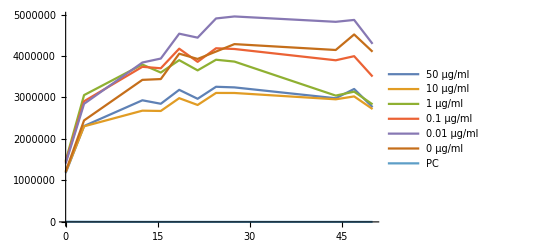

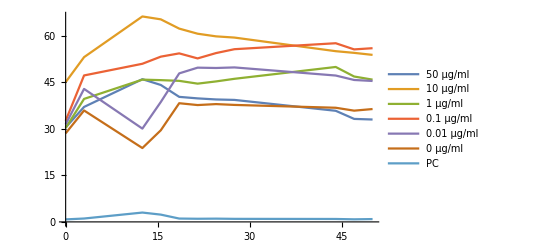

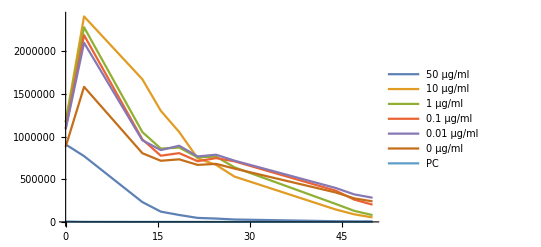

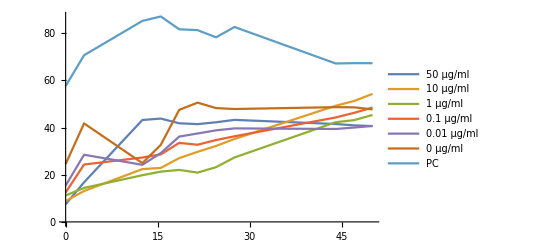

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
Print@ListLinePlot[#,PlotLegends->data⟦1,4;;10⟧]&/@% ;
```

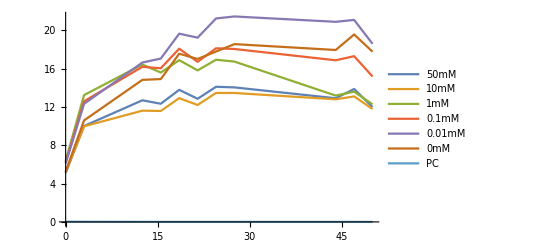

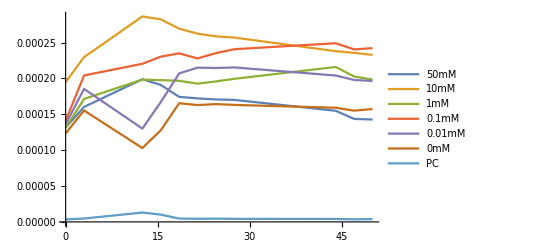

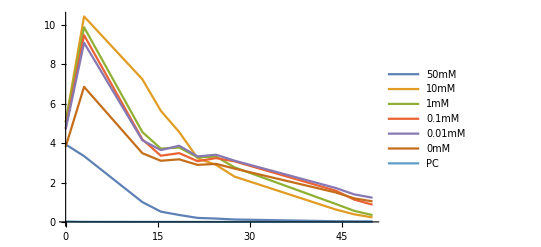

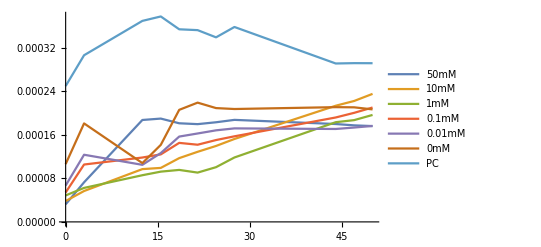

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
If[StringContainsQ[#, NumberString],StringForm["``mM",First@StringCases[#, NumberString]], "PC"]&/@ data⟦1,4;;10⟧;
Print@ListLinePlot[#,PlotLegends->%]&/@%% ;
```

```mathematica
train0 = Table[Table[{Rest@dataᵀ⟦3⟧,ConstantArray[ToExpression@First@StringCases[dataᵀ⟦i,1⟧,NumberString] ,11],Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+5}],{j,{4,11,19,26}}]
```

{{{{0.,50,5.10335},{3.,50,10.0061},{12.5,50,12.6929},{15.5,50,12.3308},{18.5,50,13.785},{21.5,50,12.8498},{24.5,50,14.1037},{27.5,50,14.0396},{44.,50,12.9059},{47.,50,13.8732},{50.,50,11.9774}},{{0.,10,5.19134},{3.,10,9.97576},{12.5,10,11.6096},{15.5,10,11.5788},{18.5,10,12.9144},{21.5,10,12.204},{24.5,10,13.4601},{27.5,10,13.4555},{44.,10,12.7957},{47.,10,13.098},{50.,10,11.782}},{{0.,1,6.36201},{3.,1,13.2344},{12.5,1,16.4245},{15.5,1,15.5884},{18.5,1,16.8814},{21.5,1,15.8152},{24.5,1,16.9262},{27.5,1,16.7323},{44.,1,13.1826},{47.,1,13.5937},{50.,1,12.268}},{{0.,0.1,6.23571},{3.,0.1,12.5926},{12.5,0.1,16.1886},{15.5,0.1,16.0354},{18.5,0.1,18.0794},{21.5,0.1,16.7069},{24.5,0.1,18.1232},{27.5,0.1,18.0472},{44.,0.1,16.8689},{47.,0.1,17.2971},{50.,0.1,15.1715}},{{0.,0.01,6.09285},{3.,0.01,12.3242},{12.5,0.01,16.6355},{15.5,0.01,17.0494},{18.5,0.01,19.6454},{21.5,0.01,19.2307},{24.5,0.01,21.2358},{27.5,0.01,21.4433},{44.,0.01,20.8841},{47.,0.01,21.0806},{50.,0.01,18.5844}},{{0.,0,5.25205},{3.,0,10.5926},{12.5,0,14.8249},{15.5,0,14.9081},{18.5,0,17.5567},{21.5,0,17.0088},{24.5,0,17.7812},{27.5,0,18.5564},{44.,0,17.9436},{47.,0,19.5644},{50.,0,17.7608}}},{{{0.,50,0.000131595},{3.,50,0.000160234},{12.5,50,0.000198927},{15.5,50,0.000190861},{18.5,50,0.000174283},{21.5,50,0.000172152},{24.5,50,0.000170659},{27.5,50,0.000170026},{44.,50,0.000154864},{47.,50,0.000143551},{50.,50,0.000142712}},{{0.,10,0.000194766},{3.,10,0.000229639},{12.5,10,0.000286351},{15.5,10,0.000282333},{18.5,10,0.000269413},{21.5,10,0.000262303},{24.5,10,0.000258614},{27.5,10,0.00025692},{44.,10,0.000237948},{47.,10,0.000235607},{50.,10,0.000232788}},{{0.,1,0.000130978},{3.,1,0.000171424},{12.5,1,0.000198289},{15.5,1,0.000197592},{18.5,1,0.000196599},{21.5,1,0.000192703},{24.5,1,0.0001958},{27.5,1,0.000199442},{44.,1,0.000215946},{47.,1,0.000202631},{50.,1,0.000198297}},{{0.,0.1,0.000140967},{3.,0.1,0.00020413},{12.5,0.1,0.000220399},{15.5,0.1,0.00023032},{18.5,0.1,0.000234889},{21.5,0.1,0.000227877},{24.5,0.1,0.000235313},{27.5,0.1,0.000240719},{44.,0.1,0.00024903},{47.,0.1,0.000240434},{50.,0.1,0.000242106}},{{0.,0.01,0.000136021},{3.,0.01,0.000185364},{12.5,0.01,0.000130042},{15.5,0.01,0.000167105},{18.5,0.01,0.00020701},{21.5,0.01,0.000214987},{24.5,0.01,0.000214523},{27.5,0.01,0.000215318},{44.,0.01,0.000204009},{47.,0.01,0.000197815},{50.,0.01,0.000196435}},{{0.,0,0.000123428},{3.,0,0.0001553},{12.5,0,0.000102935},{15.5,0,0.000127684},{18.5,0,0.00016542},{21.5,0,0.000162852},{24.5,0,0.000164199},{27.5,0,0.000163053},{44.,0,0.000159101},{47.,0,0.000155053},{50.,0,0.000157299}}},{{{0.,50,3.93374},{3.,50,3.34197},{12.5,50,1.00605},{15.5,50,0.52186},{18.5,50,0.350819},{21.5,50,0.202253},{24.5,50,0.169784},{27.5,50,0.121743},{44.,50,0.0335052},{47.,50,0.0257644},{50.,50,0.0246506}},{{0.,10,5.06891},{3.,10,10.4344},{12.5,10,7.24382},{15.5,10,5.64331},{18.5,10,4.56544},{21.5,10,3.22921},{24.5,10,2.89603},{27.5,10,2.30266},{44.,10,0.62934},{47.,10,0.385328},{50.,10,0.226597}},{{0.,1,5.06361},{3.,1,9.88569},{12.5,1,4.56232},{15.5,1,3.72307},{18.5,1,3.77475},{21.5,1,3.27746},{24.5,1,3.31563},{27.5,1,2.77192},{44.,1,0.911231},{47.,1,0.561217},{50.,1,0.345482}},{{0.,0.1,4.75052},{3.,0.1,9.48526},{12.5,0.1,4.19003},{15.5,0.1,3.36214},{18.5,0.1,3.49217},{21.5,0.1,3.082},{24.5,0.1,3.2403},{27.5,0.1,3.07624},{44.,0.1,1.5857},{47.,0.1,1.13334},{50.,0.1,0.875076}},{{0.,0.01,4.7003},{3.,0.01,9.09889},{12.5,0.01,4.14512},{15.5,0.01,3.64851},{18.5,0.01,3.86804},{21.5,0.01,3.32378},{24.5,0.01,3.41152},{27.5,0.01,3.11001},{44.,0.01,1.72228},{47.,0.01,1.39735},{50.,0.01,1.22596}},{{0.,0,3.81534},{3.,0,6.85863},{12.5,0,3.48938},{15.5,0,3.10489},{18.5,0,3.17735},{21.5,0,2.8951},{24.5,0,2.94701},{27.5,0,2.70882},{44.,0,1.49425},{47.,0,1.1979},{50.,0,1.04231}}},{{{0.,50,0.0000322428},{3.,50,0.0000726526},{12.5,50,0.000187016},{15.5,50,0.00018957},{18.5,50,0.000180957},{21.5,50,0.000179383},{24.5,50,0.000182815},{27.5,50,0.000187213},{44.,50,0.000179602},{47.,50,0.000177128},{50.,50,0.000175824}},{{0.,10,0.000038246},{3.,10,0.0000566515},{12.5,10,0.0000968557},{15.5,10,0.0000990722},{18.5,10,0.000117017},{21.5,10,0.000128608},{24.5,10,0.000139343},{27.5,10,0.000152159},{44.,10,0.000213152},{47.,10,0.0002219},{50.,10,0.000234926}},{{0.,1,0.0000485707},{3.,1,0.0000623593},{12.5,1,0.0000856522},{15.5,1,0.0000922215},{18.5,1,0.0000953831},{21.5,1,0.0000904654},{24.5,1,0.000100413},{27.5,1,0.000118219},{44.,1,0.000182946},{47.,1,0.000186749},{50.,1,0.000196257}},{{0.,0.1,0.000053917},{3.,0.1,0.000105266},{12.5,0.1,0.00011812},{15.5,0.1,0.000123888},{18.5,0.1,0.000144983},{21.5,0.1,0.000141613},{24.5,0.1,0.000150185},{27.5,0.1,0.00015704},{44.,0.1,0.000191615},{47.,0.1,0.000200126},{50.,0.1,0.000209915}},{{0.,0.01,0.0000667201},{3.,0.01,0.000123221},{12.5,0.01,0.000104711},{15.5,0.01,0.00012628},{18.5,0.01,0.000156563},{21.5,0.01,0.00016224},{24.5,0.01,0.00016801},{27.5,0.01,0.000171574},{44.,0.01,0.000170511},{47.,0.01,0.000173145},{50.,0.01,0.000176073}},{{0.,0,0.000106071},{3.,0,0.000180721},{12.5,0,0.000107903},{15.5,0,0.000141367},{18.5,0,0.0002056},{21.5,0,0.000218831},{24.5,0,0.000208833},{27.5,0,0.000207137},{44.,0,0.000210543},{47.,0,0.000210234},{50.,0,0.00020643}}}}

```mathematica
Print@ListPointPlot3D[#]&/@ train0;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Dimensions[train0]
```

{4,6,11,3}

```mathematica
max = Max[train0⟦All,All, All, 3⟧]
```

21.4433

```mathematica
train1 = ArrayReshape[#/{1,1,max}&/@Flatten[train0,2], {4,66, 3}]
```

{{{0.,50,0.237993},{3.,50,0.466629},{12.5,50,0.591929},{15.5,50,0.575043},{18.5,50,0.64286},{21.5,50,0.599245},{24.5,50,0.657722},{27.5,50,0.654732},{44.,50,0.601863},{47.,50,0.646973},{50.,50,0.558562},{0.,10,0.242096},{3.,10,0.465216},{12.5,10,0.541408},{15.5,10,0.539971},{18.5,10,0.602257},{21.5,10,0.56913},{24.5,10,0.627708},{27.5,10,0.627493},{44.,10,0.596723},{47.,10,0.610819},{50.,10,0.549451},{0.,1,0.29669},{3.,1,0.617182},{12.5,1,0.76595},{15.5,1,0.726958},{18.5,1,0.787256},{21.5,1,0.737534},{24.5,1,0.789349},{27.5,1,0.780302},{44.,1,0.614767},{47.,1,0.633935},{50.,1,0.572114},{0.,0.1,0.2908},{3.,0.1,0.587253},{12.5,0.1,0.754948},{15.5,0.1,0.747803},{18.5,0.1,0.843126},{21.5,0.1,0.779122},{24.5,0.1,0.845169},{27.5,0.1,0.841624},{44.,0.1,0.786675},{47.,0.1,0.806643},{50.,0.1,0.707515},{0.,0.01,0.284138},{3.,0.01,0.574736},{12.5,0.01,0.775792},{15.5,0.01,0.795093},{18.5,0.01,0.916157},{21.5,0.01,0.896819},{24.5,0.01,0.990322},{27.5,0.01,1.},{44.,0.01,0.97392},{47.,0.01,0.983087},{50.,0.01,0.866678},{0.,0,0.244928},{3.,0,0.493984},{12.5,0,0.691355},{15.5,0,0.695233},{18.5,0,0.818749},{21.5,0,0.793198},{24.5,0,0.829221},{27.5,0,0.865371},{44.,0,0.836792},{47.,0,0.912378},{50.,0,0.82827}},{{0.,50,6.13686×10^-6},{3.,50,7.47244×10^-6},{12.5,50,9.27689×10^-6},{15.5,50,8.90072×10^-6},{18.5,50,8.12761×10^-6},{21.5,50,8.02822×10^-6},{24.5,50,7.95864×10^-6},{27.5,50,7.9291×10^-6},{44.,50,7.22201×10^-6},{47.,50,6.69442×10^-6},{50.,50,6.65533×10^-6},{0.,10,9.08282×10^-6},{3.,10,0.0000107091},{12.5,10,0.0000133539},{15.5,10,0.0000131665},{18.5,10,0.000012564},{21.5,10,0.0000122324},{24.5,10,0.0000120604},{27.5,10,0.0000119814},{44.,10,0.0000110966},{47.,10,0.0000109874},{50.,10,0.000010856},{0.,1,6.10809×10^-6},{3.,1,7.9943×10^-6},{12.5,1,9.24711×10^-6},{15.5,1,9.21464×10^-6},{18.5,1,9.16831×10^-6},{21.5,1,8.98665×10^-6},{24.5,1,9.13107×10^-6},{27.5,1,9.30088×10^-6},{44.,1,0.0000100706},{47.,1,9.4496×10^-6},{50.,1,9.24748×10^-6},{0.,0.1,6.57393×10^-6},{3.,0.1,9.51952×10^-6},{12.5,0.1,0.0000102782},{15.5,0.1,0.0000107409},{18.5,0.1,0.000010954},{21.5,0.1,0.0000106269},{24.5,0.1,0.0000109737},{27.5,0.1,0.0000112258},{44.,0.1,0.0000116134},{47.,0.1,0.0000112125},{50.,0.1,0.0000112905},{0.,0.01,6.34328×10^-6},{3.,0.01,8.64436×10^-6},{12.5,0.01,6.06445×10^-6},{15.5,0.01,7.79289×10^-6},{18.5,0.01,9.65384×10^-6},{21.5,0.01,0.0000100258},{24.5,0.01,0.0000100042},{27.5,0.01,0.0000100413},{44.,0.01,9.51387×10^-6},{47.,0.01,9.22501×10^-6},{50.,0.01,9.16067×10^-6},{0.,0,5.75601×10^-6},{3.,0,7.24235×10^-6},{12.5,0,4.80032×10^-6},{15.5,0,5.95451×10^-6},{18.5,0,7.71431×10^-6},{21.5,0,7.59453×10^-6},{24.5,0,7.65738×10^-6},{27.5,0,7.60392×10^-6},{44.,0,7.4196×10^-6},{47.,0,7.23082×10^-6},{50.,0,7.33557×10^-6}},{{0.,50,0.183448},{3.,50,0.155851},{12.5,50,0.0469166},{15.5,50,0.0243368},{18.5,50,0.0163603},{21.5,50,0.00943198},{24.5,50,0.0079178},{27.5,50,0.00567743},{44.,50,0.0015625},{47.,50,0.00120151},{50.,50,0.00114957},{0.,10,0.236387},{3.,10,0.486604},{12.5,10,0.337813},{15.5,10,0.263174},{18.5,10,0.212908},{21.5,10,0.150593},{24.5,10,0.135055},{27.5,10,0.107384},{44.,10,0.029349},{47.,10,0.0179696},{50.,10,0.0105673},{0.,1,0.23614},{3.,1,0.461015},{12.5,1,0.212762},{15.5,1,0.173624},{18.5,1,0.176034},{21.5,1,0.152843},{24.5,1,0.154623},{27.5,1,0.129267},{44.,1,0.0424949},{47.,1,0.0261721},{50.,1,0.0161114},{0.,0.1,0.221538},{3.,0.1,0.442341},{12.5,0.1,0.1954},{15.5,0.1,0.156792},{18.5,0.1,0.162856},{21.5,0.1,0.143728},{24.5,0.1,0.15111},{27.5,0.1,0.14346},{44.,0.1,0.0739485},{47.,0.1,0.0528528},{50.,0.1,0.0408089},{0.,0.01,0.219197},{3.,0.01,0.424323},{12.5,0.01,0.193306},{15.5,0.01,0.170147},{18.5,0.01,0.180384},{21.5,0.01,0.155003},{24.5,0.01,0.159095},{27.5,0.01,0.145034},{44.,0.01,0.0803179},{47.,0.01,0.0651651},{50.,0.01,0.0571724},{0.,0,0.177927},{3.,0,0.31985},{12.5,0,0.162726},{15.5,0,0.144795},{18.5,0,0.148174},{21.5,0,0.135012},{24.5,0,0.137433},{27.5,0,0.126325},{44.,0,0.0696838},{47.,0,0.0558634},{50.,0,0.0486075}},{{0.,50,1.50363×10^-6},{3.,50,3.38813×10^-6},{12.5,50,8.72141×10^-6},{15.5,50,8.84052×10^-6},{18.5,50,8.43885×10^-6},{21.5,50,8.36546×10^-6},{24.5,50,8.52552×10^-6},{27.5,50,8.7306×10^-6},{44.,50,8.37566×10^-6},{47.,50,8.26028×10^-6},{50.,50,8.19948×10^-6},{0.,10,1.78359×10^-6},{3.,10,2.64192×10^-6},{12.5,10,4.51683×10^-6},{15.5,10,4.62019×10^-6},{18.5,10,5.45706×10^-6},{21.5,10,5.9976×10^-6},{24.5,10,6.49823×10^-6},{27.5,10,7.09586×10^-6},{44.,10,9.94024×10^-6},{47.,10,0.0000103482},{50.,10,0.0000109557},{0.,1,2.26508×10^-6},{3.,1,2.9081×10^-6},{12.5,1,3.99436×10^-6},{15.5,1,4.30071×10^-6},{18.5,1,4.44816×10^-6},{21.5,1,4.21882×10^-6},{24.5,1,4.68271×10^-6},{27.5,1,5.51311×10^-6},{44.,1,8.53161×10^-6},{47.,1,8.70896×10^-6},{50.,1,9.15236×10^-6},{0.,0.1,2.5144×10^-6},{3.,0.1,4.90905×10^-6},{12.5,0.1,5.50847×10^-6},{15.5,0.1,5.77748×10^-6},{18.5,0.1,6.76121×10^-6},{21.5,0.1,6.60405×10^-6},{24.5,0.1,7.00384×10^-6},{27.5,0.1,7.32349×10^-6},{44.,0.1,8.93588×10^-6},{47.,0.1,9.33278×10^-6},{50.,0.1,9.7893×10^-6},{0.,0.01,3.11146×10^-6},{3.,0.01,5.74635×10^-6},{12.5,0.01,4.88314×10^-6},{15.5,0.01,5.88902×10^-6},{18.5,0.01,7.30125×10^-6},{21.5,0.01,7.56601×10^-6},{24.5,0.01,7.83509×10^-6},{27.5,0.01,8.0013×10^-6},{44.,0.01,7.95171×10^-6},{47.,0.01,8.07455×10^-6},{50.,0.01,8.21109×10^-6},{0.,0,4.94657×10^-6},{3.,0,8.42784×10^-6},{12.5,0,5.03203×10^-6},{15.5,0,6.59257×10^-6},{18.5,0,9.58806×10^-6},{21.5,0,0.0000102051},{24.5,0,9.73883×10^-6},{27.5,0,9.65976×10^-6},{44.,0,9.81861×10^-6},{47.,0,9.80417×10^-6},{50.,0,9.62679×10^-6}}}

```mathematica
firsts = train0⟦All,All,1, 3⟧
```

{{5.10335,5.19134,6.36201,6.23571,6.09285,5.25205},{0.000131595,0.000194766,0.000130978,0.000140967,0.000136021,0.000123428},{3.93374,5.06891,5.06361,4.75052,4.7003,3.81534},{0.0000322428,0.000038246,0.0000485707,0.000053917,0.0000667201,0.000106071}}

```mathematica
train1//Dimensions
```

{4,66,3}

```mathematica
train2 = ArrayReshape[Table[#/{1, 1, firsts⟦i,j⟧}&/@train0⟦i, j⟧,{i,1, 4},{j, 1, 6}], {4, 66,3}]
```

{{{0.,50,1.},{3.,50,1.96068},{12.5,50,2.48717},{15.5,50,2.41622},{18.5,50,2.70117},{21.5,50,2.51791},{24.5,50,2.76362},{27.5,50,2.75106},{44.,50,2.52891},{47.,50,2.71845},{50.,50,2.34697},{0.,10,1.},{3.,10,1.92162},{12.5,10,2.23633},{15.5,10,2.2304},{18.5,10,2.48768},{21.5,10,2.35084},{24.5,10,2.5928},{27.5,10,2.59192},{44.,10,2.46482},{47.,10,2.52304},{50.,10,2.26956},{0.,1,1.},{3.,1,2.08023},{12.5,1,2.58165},{15.5,1,2.45023},{18.5,1,2.65346},{21.5,1,2.48587},{24.5,1,2.66052},{27.5,1,2.63003},{44.,1,2.07209},{47.,1,2.13669},{50.,1,1.92832},{0.,0.1,1.},{3.,0.1,2.01944},{12.5,0.1,2.59611},{15.5,0.1,2.57154},{18.5,0.1,2.89933},{21.5,0.1,2.67924},{24.5,0.1,2.90636},{27.5,0.1,2.89417},{44.,0.1,2.70521},{47.,0.1,2.77387},{50.,0.1,2.43299},{0.,0.01,1.},{3.,0.01,2.02274},{12.5,0.01,2.73034},{15.5,0.01,2.79827},{18.5,0.01,3.22434},{21.5,0.01,3.15628},{24.5,0.01,3.48536},{27.5,0.01,3.51942},{44.,0.01,3.42763},{47.,0.01,3.45989},{50.,0.01,3.0502},{0.,0,1.},{3.,0,2.01686},{12.5,0,2.82269},{15.5,0,2.83852},{18.5,0,3.34282},{21.5,0,3.2385},{24.5,0,3.38558},{27.5,0,3.53317},{44.,0,3.41649},{47.,0,3.7251},{50.,0,3.3817}},{{0.,50,1.},{3.,50,1.21763},{12.5,50,1.51167},{15.5,50,1.45037},{18.5,50,1.32439},{21.5,50,1.3082},{24.5,50,1.29686},{27.5,50,1.29204},{44.,50,1.17682},{47.,50,1.09085},{50.,50,1.08448},{0.,10,1.},{3.,10,1.17905},{12.5,10,1.47024},{15.5,10,1.4496},{18.5,10,1.38327},{21.5,10,1.34676},{24.5,10,1.32782},{27.5,10,1.31912},{44.,10,1.22172},{47.,10,1.20969},{50.,10,1.19522},{0.,1,1.},{3.,1,1.30881},{12.5,1,1.51391},{15.5,1,1.5086},{18.5,1,1.50101},{21.5,1,1.47127},{24.5,1,1.49491},{27.5,1,1.52271},{44.,1,1.64872},{47.,1,1.54706},{50.,1,1.51397},{0.,0.1,1.},{3.,0.1,1.44807},{12.5,0.1,1.56348},{15.5,0.1,1.63386},{18.5,0.1,1.66627},{21.5,0.1,1.61653},{24.5,0.1,1.66928},{27.5,0.1,1.70763},{44.,0.1,1.76659},{47.,0.1,1.7056},{50.,0.1,1.71747},{0.,0.01,1.},{3.,0.01,1.36276},{12.5,0.01,0.956043},{15.5,0.01,1.22853},{18.5,0.01,1.5219},{21.5,0.01,1.58054},{24.5,0.01,1.57713},{27.5,0.01,1.58298},{44.,0.01,1.49983},{47.,0.01,1.4543},{50.,0.01,1.44415},{0.,0,1.},{3.,0,1.25822},{12.5,0,0.833967},{15.5,0,1.03449},{18.5,0,1.34022},{21.5,0,1.31941},{24.5,0,1.33033},{27.5,0,1.32104},{44.,0,1.28902},{47.,0,1.25622},{50.,0,1.27442}},{{0.,50,1.},{3.,50,0.849565},{12.5,50,0.255748},{15.5,50,0.132663},{18.5,50,0.0891821},{21.5,50,0.0514149},{24.5,50,0.0431609},{27.5,50,0.0309483},{44.,50,0.00851739},{47.,50,0.0065496},{50.,50,0.00626646},{0.,10,1.},{3.,10,2.05851},{12.5,10,1.42907},{15.5,10,1.11332},{18.5,10,0.900674},{21.5,10,0.637062},{24.5,10,0.571331},{27.5,10,0.454271},{44.,10,0.124157},{47.,10,0.0760179},{50.,10,0.0447033},{0.,1,1.},{3.,1,1.9523},{12.5,1,0.901002},{15.5,1,0.73526},{18.5,1,0.745466},{21.5,1,0.647257},{24.5,1,0.654795},{27.5,1,0.547419},{44.,1,0.179957},{47.,1,0.110833},{50.,1,0.0682285},{0.,0.1,1.},{3.,0.1,1.99668},{12.5,0.1,0.882016},{15.5,0.1,0.707743},{18.5,0.1,0.735114},{21.5,0.1,0.648773},{24.5,0.1,0.682095},{27.5,0.1,0.64756},{44.,0.1,0.333795},{47.,0.1,0.238572},{50.,0.1,0.184207},{0.,0.01,1.},{3.,0.01,1.93581},{12.5,0.01,0.881884},{15.5,0.01,0.776228},{18.5,0.01,0.822934},{21.5,0.01,0.707142},{24.5,0.01,0.725808},{27.5,0.01,0.661662},{44.,0.01,0.366419},{47.,0.01,0.297291},{50.,0.01,0.260827},{0.,0,1.},{3.,0,1.79765},{12.5,0,0.914565},{15.5,0,0.813791},{18.5,0,0.832781},{21.5,0,0.758805},{24.5,0,0.772411},{27.5,0,0.709981},{44.,0,0.391642},{47.,0,0.313968},{50.,0,0.273188}},{{0.,50,1.},{3.,50,2.2533},{12.5,50,5.80024},{15.5,50,5.87945},{18.5,50,5.61232},{21.5,50,5.56351},{24.5,50,5.66996},{27.5,50,5.80635},{44.,50,5.57029},{47.,50,5.49356},{50.,50,5.45313},{0.,10,1.},{3.,10,1.48124},{12.5,10,2.53244},{15.5,10,2.59039},{18.5,10,3.05959},{21.5,10,3.36266},{24.5,10,3.64334},{27.5,10,3.97842},{44.,10,5.57317},{47.,10,5.80192},{50.,10,6.14249},{0.,1,1.},{3.,1,1.28389},{12.5,1,1.76345},{15.5,1,1.89871},{18.5,1,1.9638},{21.5,1,1.86255},{24.5,1,2.06735},{27.5,1,2.43396},{44.,1,3.76659},{47.,1,3.84489},{50.,1,4.04064},{0.,0.1,1.},{3.,0.1,1.95237},{12.5,0.1,2.19077},{15.5,0.1,2.29776},{18.5,0.1,2.689},{21.5,0.1,2.62649},{24.5,0.1,2.78549},{27.5,0.1,2.91262},{44.,0.1,3.55388},{47.,0.1,3.71173},{50.,0.1,3.89329},{0.,0.01,1.},{3.,0.01,1.84683},{12.5,0.01,1.5694},{15.5,0.01,1.89268},{18.5,0.01,2.34656},{21.5,0.01,2.43166},{24.5,0.01,2.51813},{27.5,0.01,2.57156},{44.,0.01,2.55562},{47.,0.01,2.5951},{50.,0.01,2.63898},{0.,0,1.},{3.,0,1.70378},{12.5,0,1.01728},{15.5,0,1.33276},{18.5,0,1.93833},{21.5,0,2.06307},{24.5,0,1.96881},{27.5,0,1.95282},{44.,0,1.98493},{47.,0,1.98202},{50.,0,1.94615}}}

## γ calculations

## Calculations with exponential models (экспоненциальные модели из курсовой работы)

### Model 1

```mathematica
train2⟦1⟧
ListPointPlot3D[%]
```

{{0.,50,0.237993},{3.,50,0.466629},{12.5,50,0.591929},{15.5,50,0.575043},{18.5,50,0.64286},{21.5,50,0.599245},{24.5,50,0.657722},{27.5,50,0.654732},{44.,50,0.601863},{47.,50,0.646973},{50.,50,0.558562},{0.,10,0.242096},{3.,10,0.465216},{12.5,10,0.541408},{15.5,10,0.539971},{18.5,10,0.602257},{21.5,10,0.56913},{24.5,10,0.627708},{27.5,10,0.627493},{44.,10,0.596723},{47.,10,0.610819},{50.,10,0.549451},{0.,1,0.29669},{3.,1,0.617182},{12.5,1,0.76595},{15.5,1,0.726958},{18.5,1,0.787256},{21.5,1,0.737534},{24.5,1,0.789349},{27.5,1,0.780302},{44.,1,0.614767},{47.,1,0.633935},{50.,1,0.572114},{0.,0.1,0.2908},{3.,0.1,0.587253},{12.5,0.1,0.754948},{15.5,0.1,0.747803},{18.5,0.1,0.843126},{21.5,0.1,0.779122},{24.5,0.1,0.845169},{27.5,0.1,0.841624},{44.,0.1,0.786675},{47.,0.1,0.806643},{50.,0.1,0.707515},{0.,0.01,0.284138},{3.,0.01,0.574736},{12.5,0.01,0.775792},{15.5,0.01,0.795093},{18.5,0.01,0.916157},{21.5,0.01,0.896819},{24.5,0.01,0.990322},{27.5,0.01,1.},{44.,0.01,0.97392},{47.,0.01,0.983087},{50.,0.01,0.866678},{0.,0,0.244928},{3.,0,0.493984},{12.5,0,0.691355},{15.5,0,0.695233},{18.5,0,0.818749},{21.5,0,0.793198},{24.5,0,0.829221},{27.5,0,0.865371},{44.,0,0.836792},{47.,0,0.912378},{50.,0,0.82827}}

-Graphics3D-

```mathematica
ClearAll[t]
```

```mathematica
k = 1;
FindFit[train2⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]},{μ ,β},{x,t}](*без ограничений на знак*)
 Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train2⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train2⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train2⟦k,;;,3⟧ , %%]]
```

{μ→-1.34635×10^10,β→8.78714×10^12}

ⅇ^(-1.74366×10^-16 t (1-ⅇ^(-8.78714×10^12 x)-8.78714×10^12 x)-0.053 x)

General::munfl: Exp[-3.1414×10^10] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

μ/β = -0.00153218

General::munfl: Exp[-2.63614×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.09839×10^14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.36201×10^14] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 1.92939

R:-9.9592

```mathematica
k = 1;
FindFit[train2⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}, Method->NMinimize]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train2⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic], PlotRange-> All]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train2⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train2⟦k,;;,3⟧ , %%]]
```

{μ→2.72304×10^-12,β→39.8253}

ⅇ^(1.71687×10^-15 t (1-ⅇ^(-39.8253 x)-39.8253 x)-0.053 x)

-Graphics3D-

μ/β = 6.83747×10^-14

General::munfl: Exp[-736.768] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-856.244] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-975.72] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.15206

R:-11.6026

```mathematica
k = 2;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→6.96741×10^-7,β→25389.3}

ⅇ^(1.08086×10^-15 t (1-ⅇ^(-25389.3 x)-25389.3 x)-0.053 x)

-Graphics3D-

μ/β = 2.74423×10^-11

General::munfl: Exp[-76167.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-317366.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-393534.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.974067

R:-22.9575

```mathematica
k = 3;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→0.0581877,β→175.437}

ⅇ^(1.89054×10^-6 t (1-ⅇ^(-175.437 x)-175.437 x)-0.053 x)

-Graphics3D-

μ/β = 0.000331672

General::munfl: Exp[-2192.97] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2719.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3245.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.319211

R:0.262703

```mathematica
k = 4;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→2.13337×10^-7,β→39265.2}

ⅇ^(1.38373×10^-16 t (1-ⅇ^(-39265.2 x)-39265.2 x)-0.053 x)

-Graphics3D-

μ/β = 5.43323×10^-12

General::munfl: Exp[-117796.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-608610.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.51674

R:-2.97476

### Model 2

```mathematica
k = 1;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→0.0000164006,β→145323.,δ→0.}

ⅇ^(7.76587×10^-16 (1-ⅇ^(-145323. t)-145323. t) t-0.053 x)

-Graphics3D-

General::munfl: Exp[-7.26616×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.15206

R:-11.6026

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→9.73901,β→199707.,δ→0.000192393}

ⅇ^(2.4419×10^-10 (1-ⅇ^(-199707. t)-199707. t) t+(-0.053-0.000192393 t) x)

General::munfl: Exp[-713.953] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

General::munfl: Exp[-9.98536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.321901

R:0.263777

### Model 3

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ* t+0.053) x], δ>0},{δ},{x,t}]
Exp[-(δ* t+0.053) x]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{δ→0.000331456}

ⅇ^((-0.053-0.000331456 t) x)

-Graphics3D-

MAE: 0.319214

R:0.2627

## Calculation with linear models (линейные модели)

{{0.,1.17887×10^6},{3.,2.3114×10^6},{12.5,2.93206×10^6},{15.5,2.84842×10^6},{18.5,3.18434×10^6},{21.5,2.9683×10^6},{24.5,3.25796×10^6},{27.5,3.24315×10^6},{44.,2.98127×10^6},{47.,3.20472×10^6},{50.,2.76678×10^6}}

FittedModel[2.31832×10^6+20362.7 x]

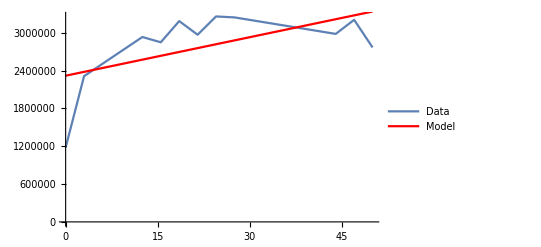

MAE: 378326.

R:0.325236

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦4⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦4⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦4⟧, %%]]
```

{{0.,1.17092×10^6},{3.,2.41034×10^6},{12.5,1.67332×10^6},{15.5,1.3036×10^6},{18.5,1.05462×10^6},{21.5,745948.},{24.5,668983.},{27.5,531915.},{44.,145377.},{47.,89010.8},{50.,52343.9}}

FittedModel[1.79817×10^6-37627. x]

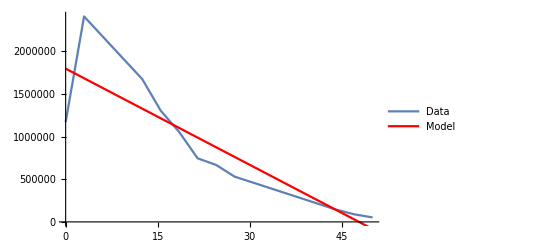

MAE: 246692.

R:0.768515

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦20⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦20⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦20⟧, %%]]
```

### Calculating dynamics of data

```mathematica
slope[lin_]:= ArcTan[D[Normal[lin],x]]
```

Data dynamics: 1.52245×10^6

FittedModel[2.2078×10^6+20065.3 x]

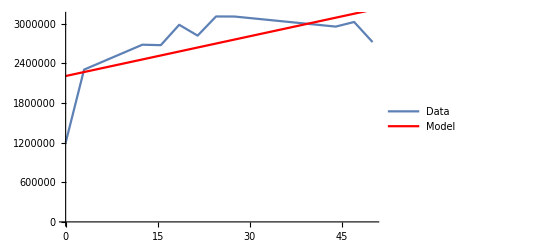

Angle of inclination: 1.57075

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦5⟧](*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦5⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```

Data dynamics: 2.88953×10^6

FittedModel[2.52766×10^6+44962. x]

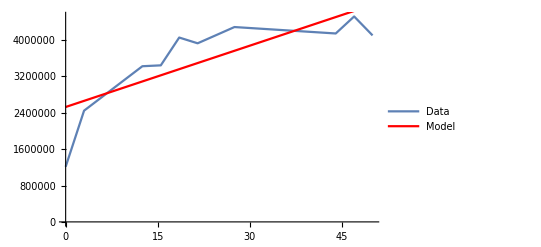

Angle of inclination: 1.57077

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦9⟧] (*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦9⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```